```mathematica
{τl=40,b=0.25, kc =60, μ=0.06,σ=0.01,ϵ=0,k=0.1,τe=720,ϕl=1/8,ϕe=1/9,γ0=0.39,ν=0.003,γ=0.48,θ1=1,δe=1,αe=2.6*^-6,δl=1,αl=5.6*^-6}; 
systemcase0 = {b*n*(kc-n)/kc-μ*n-σ*prev*n -ν*(pars+pari)==0 &&
αe*δe*(1-prev)*eggs-(γ0+γ*(pari)/(prev*n))*prev-prev*b*(kc-n)/kc-ν/n*((pari*(1-prev))-pars*prev)-prev*σ*(1-prev)==0&&
τe*prev*n-ϕe*eggs==0&&
αl*δl*larv*n*(1-prev)+(γ0+γ*pari/(prev*n))*pari-(μ+ν+ϵ)*pars-αe*δe*eggs*pars-pars^2*ν*(k+1)/(n*(1-prev)*k)==0&&
αl*δl*larv*n*prev-(γ0+γ*pari/(prev*n))*pari-(μ+ν+σ+ϵ)*pari +αe*δe*eggs*pars-pari^2*ν*(k+1)/(n*prev*k)==0&&
τl*pars+τl*pari-ϕl*larv==0 && 
(pars+pari)/n == hpolymb};
Solve[systemcase0,{n,prev,eggs,pars,pari,larv,hpolymb}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.667,prev→0.388745,eggs→112519.,pars→0.,pari→0.,larv→0.,hpolymb→0.},{n→43.7693,prev→1.01961,eggs→289186.,pars→6.37139,pari→-43.8383,larv→-11989.4,hpolymb→-0.856009},{n→36.2795,prev→5.04774,eggs→1.18668×10^6,pars→971.686,pari→-1112.47,larv→-45051.8,hpolymb→-3.88062},{n→0.00712461-0.108156 ⅈ,prev→18.49-3.45715 ⅈ,eggs→-1569.31-13118.4 ⅈ,pars→0.910799-1.99385 ⅈ,pari→0.363861+1.89425 ⅈ,larv→407.891-31.8733 ⅈ,hpolymb→1.68994+11.674 ⅈ},{n→0.00712461+0.108156 ⅈ,prev→18.49+3.45715 ⅈ,eggs→-1569.31+13118.4 ⅈ,pars→0.910799+1.99385 ⅈ,pari→0.363861-1.89425 ⅈ,larv→407.891+31.8733 ⅈ,hpolymb→1.68994-11.674 ⅈ},{n→-1.46701,prev→19.6113,eggs→-186429.,pars→0.,pari→0.,larv→0.,hpolymb→0.},{n→-7.88385,prev→22.4747,eggs→-1.14817×10^6,pars→882.644,pari→-877.656,larv→1596.17,hpolymb→-0.632692}}

```mathematica
{δemin=1.3*^-1,δemax=2.6*^-1,αemin=1*^-5,αemax=2*^-5,δlmin=2.8*^-1,δlmax=5.6*^-1,αlmin=1*^-5,αlmax=2*^-5};
```

```mathematica
{δp1=δemin+(δemax-δemin)*E^(-θ1*prov),δp2=δlmin+(δlmax-δlmin)*E^(-θ2*prov),αp1=αemax-(αemax-αemin)*E^(-θ3*prov),αp2=αlmax-(αlmax-αlmin)*E^(-θ3*prov)};
```

```mathematica
systemehung = {b*n*(kc-n)/kc-μ*n-σ*prev*n -ν*(pars+pari)==0 &&
αp1*δp1*(1-prev)*eggs-(γ0+γ*(pari)/(prev*n))*prev-prev*b*(kc-n)/kc-ν/n*((pari*(1-prev))-pars*prev)-prev*σ*(1-prev)==0&&
τe*prev*n-ϕe*eggs==0&&
αp2*δp2*larv*n*(1-prev)+(γ0+γ*pari/(prev*n))*pari-(μ+ν+ϵ)*pars-αp1*δp1*eggs*pars-pars^2*ν*(k+1)/(n*(1-prev)*k)==0&&
αp2*δp2*larv*n*prev-(γ0+γ*pari/(prev*n))*pari-(μ+ν+σ+ϵ)*pari +αp1*δp1*eggs*pars-pari^2*ν*(k+1)/(n*prev*k)==0&&
τl*pars+τl*pari-ϕl*larv==0 && 
(pars+pari)/n == hpolymb};
```

```mathematica
data0= Table[Table[Solve[systemehung,{n,prev,eggs,pars,pari,larv,hpolymb}][[1]],{prov,0,1}],{θ2,0.5,5.5,0.5},{θ3,0,5,0.5}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3916,prev→0.0730047,eggs→21473.4,pars→1.92456,pari→0.17058,larv→670.443,hpolymb→0.0461569}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.6555,prev→-0.313969,eggs→-92887.1,pars→59.1993,pari→-14.9356,larv→14164.4,hpolymb→0.969517}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.5451,prev→-0.418038,eggs→-123376.,pars→96.6881,pari→-29.7475,larv→21421.,hpolymb→1.46977}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.441,prev→-0.462659,eggs→-136233.,pars→119.327,pari→-39.2119,larv→25637.,hpolymb→1.76307}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3691,prev→-0.485245,eggs→-142658.,pars→132.959,pari→-45.0264,larv→28138.5,hpolymb→1.93816}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.323,prev→-0.497623,eggs→-146148.,pars→141.183,pari→-48.5671,larv→29637.,hpolymb→2.04346}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.2942,prev→-0.504702,eggs→-148133.,pars→146.153,pari→-50.7175,larv→30539.4,hpolymb→2.10701}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.2765,prev→-0.508849,eggs→-149292.,pars→149.161,pari→-52.0225,larv→31084.3,hpolymb→2.14545}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.2657,prev→-0.511312,eggs→-149979.,pars→150.983,pari→-52.8141,larv→31414.,hpolymb→2.16872}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.2591,prev→-0.512788,eggs→-150390.,pars→152.087,pari→-53.2943,larv→31613.7,hpolymb→2.18283}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.255,prev→-0.513676,eggs→-150637.,pars→152.756,pari→-53.5856,larv→31734.6,hpolymb→2.19138}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.1297,prev→0.0755183,eggs→22084.6,pars→16.6397,pari→1.48124,larv→5798.71,hpolymb→0.401531}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.1253,prev→-0.0555557,eggs→-16245.2,pars→40.3688,pari→-2.26208,larv→12194.2,hpolymb→0.844465}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.0733,prev→-0.111009,eggs→-32422.9,pars→55.5089,pari→-5.85629,larv→15888.8,hpolymb→1.1016}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.0301,prev→-0.138917,eggs→-40535.4,pars→64.8065,pari→-8.31408,larv→18077.6,hpolymb→1.25455}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.0006,prev→-0.154168,eggs→-44956.1,pars→70.4678,pari→-9.88,larv→19388.1,hpolymb→1.34638}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.9816,prev→-0.162876,eggs→-47475.4,pars→73.9064,pari→-10.8529,larv→20177.1,hpolymb→1.40176}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.9698,prev→-0.167973,eggs→-48948.,pars→75.9932,pari→-11.4507,larv→20653.6,hpolymb→1.43524}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.9624,prev→-0.170999,eggs→-49821.7,pars→77.2591,pari→-11.8159,larv→20941.8,hpolymb→1.45551}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.9579,prev→-0.172811,eggs→-50344.7,pars→78.0271,pari→-12.0383,larv→21116.4,hpolymb→1.46779}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.9552,prev→-0.173902,eggs→-50659.3,pars→78.4929,pari→-12.1736,larv→21222.2,hpolymb→1.47523}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7959,prev→0.317284,eggs→92100.6,pars→1.735,pari→0.914241,larv→847.757,hpolymb→0.0591402}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.8606,prev→0.167861,eggs→48796.7,pars→17.1953,pari→3.77403,larv→6710.17,hpolymb→0.467432}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.8419,prev→0.105066,eggs→30529.6,pars→27.9838,pari→3.52784,larv→10083.7,hpolymb→0.702729}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.817,prev→0.0735694,eggs→21365.6,pars→34.7983,pari→2.94982,larv→12079.4,hpolymb→0.842272}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.798,prev→0.0563877,eggs→16368.8,pars→39.,pari→2.48012,larv→13273.6,hpolymb→0.925937}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7852,prev→0.0465869,eggs→13519.9,pars→41.5685,pari→2.15786,larv→13992.4,hpolymb→0.976358}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.777,prev→0.040854,eggs→11854.,pars→43.1328,pari→1.94987,larv→14426.5,hpolymb→1.00683}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7719,prev→0.0374511,eggs→10865.4,pars→44.0838,pari→1.81936,larv→14689.,hpolymb→1.02527}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7688,prev→0.0354139,eggs→10273.6,pars→44.6613,pari→1.73865,larv→14848.,hpolymb→1.03644}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7668,prev→0.0341879,eggs→9917.53,pars→45.0119,pari→1.68914,larv→14944.3,hpolymb→1.04321}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6961,prev→0.304673,eggs→88242.5,pars→7.21091,pari→3.50987,larv→3430.65,hpolymb→0.23986}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6982,prev→0.237182,eggs→68698.5,pars→15.4161,pari→5.22673,larv→6605.69,hpolymb→0.461826}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6848,prev→0.203383,eggs→58891.,pars→20.7714,pari→5.73605,larv→8482.37,hpolymb→0.593209}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6723,prev→0.184962,eggs→53542.3,pars→24.1194,pari→5.89609,larv→9604.97,hpolymb→0.671904}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6634,prev→0.17446,eggs→50492.1,pars→26.1804,pari→5.94622,larv→10280.5,hpolymb→0.719306}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6575,prev→0.168319,eggs→48708.3,pars→27.4404,pari→5.96084,larv→10688.4,hpolymb→0.747942}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6538,prev→0.164675,eggs→47649.7,pars→28.208,pari→5.9642,larv→10935.1,hpolymb→0.76527}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6515,prev→0.162493,eggs→47016.,pars→28.6748,pari→5.96428,larv→11084.5,hpolymb→0.775765}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.65,prev→0.16118,eggs→46634.6,pars→28.9583,pari→5.96362,larv→11175.,hpolymb→0.782125}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5949,prev→0.388062,eggs→112140.,pars→2.66007,pari→1.90715,larv→1461.51,hpolymb→0.102416}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6099,prev→0.317683,eggs→91833.4,pars→9.31578,pari→4.78898,larv→4513.52,hpolymb→0.31618}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.6035,prev→0.282453,eggs→81637.6,pars→13.8018,pari→5.93869,larv→6316.96,hpolymb→0.442578}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.595,prev→0.26326,eggs→76075.8,pars→16.6431,pari→6.46798,larv→7395.53,hpolymb→0.518242}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5885,prev→0.252321,eggs→72903.9,pars→18.4032,pari→6.73592,larv→8044.53,hpolymb→0.563804}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.584,prev→0.245925,eggs→71048.7,pars→19.483,pari→6.88056,larv→8436.34,hpolymb→0.591323}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5811,prev→0.242129,eggs→69947.7,pars→20.1421,pari→6.96205,larv→8673.32,hpolymb→0.607973}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5793,prev→0.239857,eggs→69288.6,pars→20.5433,pari→7.00925,larv→8816.83,hpolymb→0.618057}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5782,prev→0.23849,eggs→68891.9,pars→20.7872,pari→7.03707,larv→8903.78,hpolymb→0.624168}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5331,prev→0.438751,eggs→126612.,pars→0.454473,pari→0.40712,larv→275.71,hpolymb→0.0193473}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5559,prev→0.366631,eggs→105854.,pars→6.1767,pari→3.98441,larv→3251.55,hpolymb→0.228053}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5537,prev→0.330526,eggs→95425.6,pars→10.1411,pari→5.5152,larv→5010.,hpolymb→0.351402}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5478,prev→0.310859,eggs→89735.7,pars→12.6788,pari→6.2637,larv→6061.6,hpolymb→0.425218}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5427,prev→0.299651,eggs→86490.3,pars→14.259,pari→6.66075,larv→6694.33,hpolymb→0.469657}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5391,prev→0.293098,eggs→84592.1,pars→15.2311,pari→6.88239,larv→7076.31,hpolymb→0.496496}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5367,prev→0.28921,eggs→83465.5,pars→15.8253,pari→7.01012,larv→7307.35,hpolymb→0.512733}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5352,prev→0.286883,eggs→82791.,pars→16.1874,pari→7.08521,larv→7447.25,hpolymb→0.522567}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5343,prev→0.285482,eggs→82385.2,pars→16.4077,pari→7.12988,larv→7532.01,hpolymb→0.528526}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5186,prev→0.450588,eggs→129986.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.523,prev→0.396357,eggs→114352.,pars→4.47922,pari→3.2986,larv→2488.9,hpolymb→0.174692}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5234,prev→0.359722,eggs→103784.,pars→8.12922,pari→5.05766,larv→4219.8,hpolymb→0.296178}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.519,prev→0.339767,eggs→98017.1,pars→10.4843,pari→5.93731,larv→5254.91,hpolymb→0.368867}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5148,prev→0.328395,eggs→94727.5,pars→11.9563,pari→6.41154,larv→5877.71,hpolymb→0.412623}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5117,prev→0.321747,eggs→92803.3,pars→12.8636,pari→6.67919,larv→6253.68,hpolymb→0.439048}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5097,prev→0.317802,eggs→91661.3,pars→13.4189,pari→6.83454,larv→6481.09,hpolymb→0.455034}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5083,prev→0.315441,eggs→90977.6,pars→13.7574,pari→6.92628,larv→6618.79,hpolymb→0.464715}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5075,prev→0.31402,eggs→90566.2,pars→13.9634,pari→6.98102,larv→6702.22,hpolymb→0.470582}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5186,prev→0.450588,eggs→129986.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5029,prev→0.414399,eggs→119504.,pars→3.52562,pari→2.81003,larv→2027.41,hpolymb→0.142365}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.505,prev→0.377444,eggs→108852.,pars→6.9857,pari→4.70643,larv→3741.48,hpolymb→0.262715}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5014,prev→0.357314,eggs→103038.,pars→9.23049,pari→5.66493,larv→4766.53,hpolymb→0.334718}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4978,prev→0.345842,eggs→99722.1,pars→10.6372,pari→6.18555,larv→5383.28,hpolymb→0.378058}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.495,prev→0.339136,eggs→97782.3,pars→11.5054,pari→6.48084,larv→5755.6,hpolymb→0.40423}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4932,prev→0.335157,eggs→96631.,pars→12.0372,pari→6.65279,larv→5980.79,hpolymb→0.420064}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.492,prev→0.332775,eggs→95941.7,pars→12.3616,pari→6.75453,larv→6117.15,hpolymb→0.429653}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4912,prev→0.331342,eggs→95526.9,pars→12.559,pari→6.81532,larv→6199.78,hpolymb→0.435463}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5186,prev→0.450588,eggs→129986.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4908,prev→0.425346,eggs→122627.,pars→2.97518,pari→2.48705,larv→1747.91,hpolymb→0.122772}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4938,prev→0.388197,eggs→111925.,pars→6.32035,pari→4.46631,larv→3451.73,hpolymb→0.242431}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4908,prev→0.367961,eggs→106083.,pars→8.49844,pari→5.47238,larv→4470.66,hpolymb→0.314016}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4875,prev→0.356429,eggs→102751.,pars→9.86566,pari→6.02098,larv→5083.72,hpolymb→0.357104}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4849,prev→0.349687,eggs→100802.,pars→10.7103,pari→6.33294,larv→5453.82,hpolymb→0.383123}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4832,prev→0.345687,eggs→99644.7,pars→11.2278,pari→6.51489,larv→5677.67,hpolymb→0.398864}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4821,prev→0.343293,eggs→98952.,pars→11.5436,pari→6.62266,larv→5813.21,hpolymb→0.408396}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4814,prev→0.341852,eggs→98535.2,pars→11.7359,pari→6.68709,larv→5895.34,hpolymb→0.414172}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5186,prev→0.450588,eggs→129986.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4834,prev→0.431988,eggs→124521.,pars→2.6516,pari→2.28135,larv→1578.54,hpolymb→0.110894}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.487,prev→0.394721,eggs→113788.,pars→5.92718,pari→4.31071,larv→3276.13,hpolymb→0.230132}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4843,prev→0.374421,eggs→107930.,pars→8.06489,pari→5.34553,larv→4291.34,hpolymb→0.301464}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4812,prev→0.362852,eggs→104588.,pars→9.4082,pari→5.91104,larv→4902.16,hpolymb→0.344398}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4788,prev→0.356089,eggs→102633.,pars→10.2385,pari→6.23308,larv→5270.9,hpolymb→0.370325}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4771,prev→0.352076,eggs→101472.,pars→10.7475,pari→6.42108,larv→5493.93,hpolymb→0.386009}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.476,prev→0.349674,eggs→100778.,pars→11.0581,pari→6.53249,larv→5628.98,hpolymb→0.395507}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4753,prev→0.348229,eggs→100360.,pars→11.2472,pari→6.59912,larv→5710.81,hpolymb→0.401263}}},{{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→45.3143,prev→0.11904,eggs→34954.4,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.7369,prev→0.359634,eggs→104256.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.5186,prev→0.450588,eggs→129986.,pars→0.,pari→0.,larv→0.,hpolymb→0.}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4789,prev→0.436016,eggs→125670.,pars→2.45911,pari→2.15299,larv→1475.87,hpolymb→0.103692}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4828,prev→0.398678,eggs→114919.,pars→5.69253,pari→4.21267,larv→3169.67,hpolymb→0.222675}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4804,prev→0.378339,eggs→109050.,pars→7.80577,pari→5.2649,larv→4182.62,hpolymb→0.293852}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4774,prev→0.366748,eggs→105702.,pars→9.1346,pari→5.84064,larv→4792.08,hpolymb→0.336694}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.475,prev→0.359972,eggs→103743.,pars→9.95624,pari→6.16878,larv→5160.,hpolymb→0.362563}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4734,prev→0.355952,eggs→102581.,pars→10.46,pari→6.36043,larv→5382.54,hpolymb→0.378213}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4724,prev→0.353545,eggs→101885.,pars→10.7675,pari→6.47405,larv→5517.29,hpolymb→0.387691}},{{n→45.1424,prev→0.0310409,eggs→9080.16,pars→23.2141,pari→0.80348,larv→7685.62,hpolymb→0.53204},{n→44.4717,prev→0.352097,eggs→101466.,pars→10.9547,pari→6.54202,larv→5598.94,hpolymb→0.393434}}}}

```mathematica
resprev =Table[(prev/.data0[[i]][[j]][[2]])-(prev/.data0[[i]][[j]][[1]]),{i,1,11},{j,1,11}]
```

{{0.0419638,-0.34501,-0.449079,-0.4937,-0.516286,-0.528664,-0.535743,-0.539889,-0.542353,-0.543828,-0.544717},{0.0879989,0.0444775,-0.0865966,-0.14205,-0.169958,-0.185209,-0.193917,-0.199014,-0.20204,-0.203852,-0.204943},{0.0879989,0.286243,0.136821,0.0740252,0.0425285,0.0253468,0.015546,0.0098131,0.00641029,0.00437303,0.00314701},{0.0879989,0.328593,0.273632,0.206141,0.172342,0.153921,0.143419,0.137278,0.133634,0.131452,0.130139},{0.0879989,0.328593,0.357021,0.286643,0.251412,0.232219,0.22128,0.214884,0.211088,0.208816,0.207449},{0.0879989,0.328593,0.40771,0.33559,0.299485,0.279819,0.26861,0.262058,0.258169,0.255842,0.254442},{0.0879989,0.328593,0.419547,0.365316,0.328682,0.308727,0.297354,0.290706,0.286761,0.2844,0.282979},{0.0879989,0.328593,0.419547,0.383358,0.346403,0.326273,0.314802,0.308095,0.304116,0.301734,0.300301},{0.0879989,0.328593,0.419547,0.394306,0.357156,0.33692,0.325388,0.318647,0.314646,0.312252,0.310811},{0.0879989,0.328593,0.419547,0.400947,0.36368,0.34338,0.331811,0.325048,0.321035,0.318633,0.317188},{0.0879989,0.328593,0.419547,0.404975,0.367637,0.347298,0.335707,0.328931,0.324911,0.322504,0.321056}}

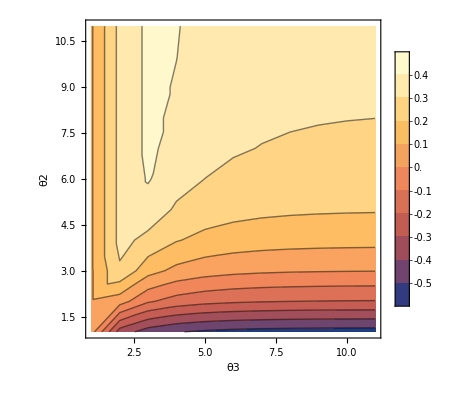

```mathematica
ListContourPlot[resprev,PlotLegends->Automatic,FrameLabel->{"θ3","θ2"},PlotRange->All]
```

```mathematica
reshpolymb =Table[(hpolymb/.data0[[i]][[j]][[2]])-(hpolymb/.data0[[i]][[j]][[1]]),{i,1,11},{j,1,11}]
```

{{-0.485883,0.437478,0.937728,1.23103,1.40612,1.51142,1.57497,1.61341,1.63669,1.65079,1.65934},{-0.53204,-0.130508,0.312426,0.569558,0.722508,0.814339,0.869721,0.903202,0.92347,0.935748,0.94319},{-0.53204,-0.472899,-0.0646071,0.170689,0.310233,0.393897,0.444318,0.474787,0.493227,0.504397,0.511167},{-0.53204,-0.53204,-0.29218,-0.0702139,0.0611694,0.139865,0.187266,0.215902,0.23323,0.243725,0.250086},{-0.53204,-0.53204,-0.429624,-0.21586,-0.0894619,-0.0137971,0.0317641,0.0592832,0.0759336,0.0860178,0.0921288},{-0.53204,-0.53204,-0.512692,-0.303987,-0.180638,-0.106822,-0.0623825,-0.0355438,-0.0193063,-0.00947245,-0.0035133},{-0.53204,-0.53204,-0.53204,-0.357347,-0.235861,-0.163172,-0.119416,-0.0929917,-0.0770054,-0.067324,-0.0614573},{-0.53204,-0.53204,-0.53204,-0.389675,-0.269324,-0.197322,-0.153981,-0.127809,-0.111976,-0.102387,-0.0965763},{-0.53204,-0.53204,-0.53204,-0.409267,-0.289609,-0.218024,-0.174936,-0.148917,-0.133176,-0.123643,-0.117867},{-0.53204,-0.53204,-0.53204,-0.421145,-0.301907,-0.230576,-0.187641,-0.161715,-0.146031,-0.136532,-0.130777},{-0.53204,-0.53204,-0.53204,-0.428348,-0.309365,-0.238187,-0.195346,-0.169476,-0.153826,-0.144349,-0.138606}}

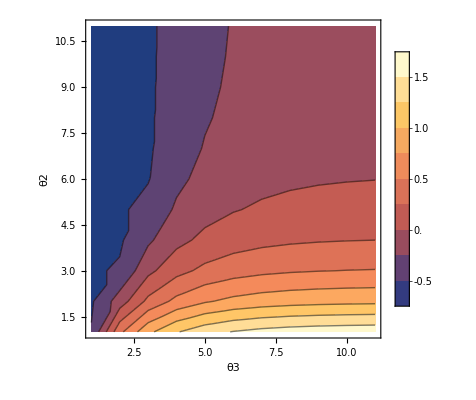

```mathematica
ListContourPlot[reshpolymb,PlotLegends->Automatic,FrameLabel->{"θ3","θ2"},PlotRange->All]
```

```mathematica
systemcase01={b*n*(kc-n)/kc-μ*n-σ*prev*n-ν*(pars+pari)==0&&αe*δe*(1-prev)*eggs-γ0*prev-prev*b*(kc-n)/kc-ν/n*((pari*(1-prev))-pars*prev)-prev*σ*(1-prev)==0&&τe*prev*n-ϕe*eggs==0&&αl*δl*larv*n*(1-prev)+γ0*pari-(μ+ν+ϵ)*pars-αe*δe*eggs*pars-pars^2*ν*(k+1)/(n*(1-prev)*k)==0&&αl*δl*larv*n*prev-γ0*pari-(μ+ν+σ+ϵ)*pari+αe*δe*eggs*pars-pari^2*ν*(k+1)/(n*prev*k)==0&&τl*pars+τl*pari-ϕl*larv==0&&(pars+pari)/n==hpolymb};
```

```mathematica
Solve[systemcase01,{n,prev,eggs,pars,pari,larv,hpolymb}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→-1.46701,prev→19.6113,eggs→-186429.,pars→0.,pari→0.,larv→0.,hpolymb→0.},{n→-1.45165,prev→19.9914,eggs→-188053.,pars→45.2091,pari→-43.3388,larv→598.486,hpolymb→-1.28837},{n→-1.27438,prev→22.1011,eggs→-182510.,pars→-54.2789,pari→65.1965,larv→3493.63,hpolymb→-8.56701},{n→12.0798,prev→-0.920517,eggs→-72055.1,pars→343.19,pari→256.259,larv→191824.,hpolymb→49.6243},{n→44.4096,prev→0.383572,eggs→110382.,pars→9.72143,pari→6.92271,larv→5326.12,hpolymb→0.374787},{n→44.667,prev→0.388745,eggs→112519.,pars→0.,pari→0.,larv→0.,hpolymb→0.},{n→53.7192-1.45082 ⅈ,prev→0.535201-0.0621039 ⅈ,eggs→185720.-26650. ⅈ,pars→-398.647-341.959 ⅈ,pari→-299.739+480.274 ⅈ,larv→-223483.+44260.9 ⅈ,hpolymb→-13.0607+2.22204 ⅈ},{n→53.7192+1.45082 ⅈ,prev→0.535201+0.0621039 ⅈ,eggs→185720.+26650. ⅈ,pars→-398.647+341.959 ⅈ,pari→-299.739-480.274 ⅈ,larv→-223483.-44260.9 ⅈ,hpolymb→-13.0607-2.22204 ⅈ}}

```mathematica
systemeupt={b*n*(kc-n)/kc-μ*n-σ*prev*n-ν*(pars+pari)==0&&αp1*δp1*(1-prev)*eggs-γ0*prev-prev*b*(kc-n)/kc-ν/n*((pari*(1-prev))-pars*prev)-prev*σ*(1-prev)==0&&τe*prev*n-ϕe*eggs==0&&αp2*δp2*larv*n*(1-prev)+γ0*pari-(μ+ν+ϵ)*pars-αp1*δp1*eggs*pars-pars^2*ν*(k+1)/(n*(1-prev)*k)==0&&αp2*δp2*larv*n*prev-γ0*pari-(μ+ν+σ+ϵ)*pari+αp1*δp1*eggs*pars-pari^2*ν*(k+1)/(n*prev*k)==0&&τl*pars+τl*pari-ϕl*larv==0&&(pars+pari)/n==hpolymb};
```

```mathematica
data2 = Table[Table[Solve[systemeupt,{n,prev,eggs,pars,pari,larv,hpolymb}][[5]],{prov,0,1}],{θ2,0.5,5.5,0.5},{θ3,0,5,0.5}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
resprev2 =Table[(prev/.data2[[i]][[j]][[2]])-(prev/.data2[[i]][[j]][[1]]),{i,1,11},{j,1,11}]
```

{{-0.265051,-0.0335702,0.0536751,0.0954151,0.117639,0.130146,0.137406,0.141696,0.144257,0.145796,0.146724},{-0.264532,-0.0279447,0.0593164,0.101065,0.123293,0.135803,0.143065,0.147355,0.149917,0.151456,0.152385},{-0.264532,-0.0245314,0.0627387,0.104492,0.126723,0.139235,0.146497,0.150788,0.153351,0.15489,0.155818},{-0.264532,-0.0239384,0.0648148,0.106571,0.128803,0.141316,0.148579,0.152871,0.155433,0.156973,0.157901},{-0.264532,-0.0239384,0.066074,0.107832,0.130065,0.142579,0.149842,0.154134,0.156696,0.158236,0.159165},{-0.264532,-0.0239384,0.0668379,0.108597,0.130831,0.143345,0.150608,0.1549,0.157463,0.159002,0.159931},{-0.264532,-0.0239384,0.0670161,0.109061,0.131295,0.143809,0.151073,0.155365,0.157927,0.159467,0.160396},{-0.264532,-0.0239384,0.0670161,0.109342,0.131577,0.144091,0.151355,0.155647,0.158209,0.159749,0.160677},{-0.264532,-0.0239384,0.0670161,0.109513,0.131748,0.144262,0.151526,0.155817,0.15838,0.15992,0.160848},{-0.264532,-0.0239384,0.0670161,0.109616,0.131851,0.144365,0.151629,0.155921,0.158484,0.160024,0.160952},{-0.264532,-0.0239384,0.0670161,0.109679,0.131914,0.144428,0.151692,0.155984,0.158547,0.160086,0.161015}}

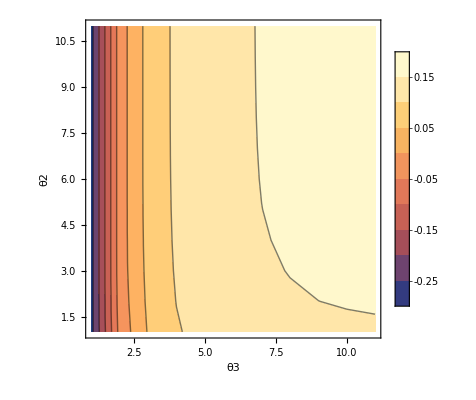

```mathematica
ListContourPlot[resprev2,PlotLegends->Automatic,FrameLabel->{"θ3","θ2"},PlotRange->All]
```

{{0.0419638,-0.34501,-0.449079,-0.4937,-0.516286,-0.528664,-0.535743,-0.539889,-0.542353,-0.543828,-0.544717},{0.0879989,0.0444775,-0.0865966,-0.14205,-0.169958,-0.185209,-0.193917,-0.199014,-0.20204,-0.203852,-0.204943},{0.0879989,0.286243,0.136821,0.0740252,0.0425285,0.0253468,0.015546,0.0098131,0.00641029,0.00437303,0.00314701},{0.0879989,0.328593,0.273632,0.206141,0.172342,0.153921,0.143419,0.137278,0.133634,0.131452,0.130139},{0.0879989,0.328593,0.357021,0.286643,0.251412,0.232219,0.22128,0.214884,0.211088,0.208816,0.207449},{0.0879989,0.328593,0.40771,0.33559,0.299485,0.279819,0.26861,0.262058,0.258169,0.255842,0.254442},{0.0879989,0.328593,0.419547,0.365316,0.328682,0.308727,0.297354,0.290706,0.286761,0.2844,0.282979},{0.0879989,0.328593,0.419547,0.383358,0.346403,0.326273,0.314802,0.308095,0.304116,0.301734,0.300301},{0.0879989,0.328593,0.419547,0.394306,0.357156,0.33692,0.325388,0.318647,0.314646,0.312252,0.310811},{0.0879989,0.328593,0.419547,0.400947,0.36368,0.34338,0.331811,0.325048,0.321035,0.318633,0.317188},{0.0879989,0.328593,0.419547,0.404975,0.367637,0.347298,0.335707,0.328931,0.324911,0.322504,0.321056}}

{{-0.265051,-0.0335702,0.0536751,0.0954151,0.117639,0.130146,0.137406,0.141696,0.144257,0.145796,0.146724},{-0.264532,-0.0279447,0.0593164,0.101065,0.123293,0.135803,0.143065,0.147355,0.149917,0.151456,0.152385},{-0.264532,-0.0245314,0.0627387,0.104492,0.126723,0.139235,0.146497,0.150788,0.153351,0.15489,0.155818},{-0.264532,-0.0239384,0.0648148,0.106571,0.128803,0.141316,0.148579,0.152871,0.155433,0.156973,0.157901},{-0.264532,-0.0239384,0.066074,0.107832,0.130065,0.142579,0.149842,0.154134,0.156696,0.158236,0.159165},{-0.264532,-0.0239384,0.0668379,0.108597,0.130831,0.143345,0.150608,0.1549,0.157463,0.159002,0.159931},{-0.264532,-0.0239384,0.0670161,0.109061,0.131295,0.143809,0.151073,0.155365,0.157927,0.159467,0.160396},{-0.264532,-0.0239384,0.0670161,0.109342,0.131577,0.144091,0.151355,0.155647,0.158209,0.159749,0.160677},{-0.264532,-0.0239384,0.0670161,0.109513,0.131748,0.144262,0.151526,0.155817,0.15838,0.15992,0.160848},{-0.264532,-0.0239384,0.0670161,0.109616,0.131851,0.144365,0.151629,0.155921,0.158484,0.160024,0.160952},{-0.264532,-0.0239384,0.0670161,0.109679,0.131914,0.144428,0.151692,0.155984,0.158547,0.160086,0.161015}}

ColorData::notent: ColorBlindSafe is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

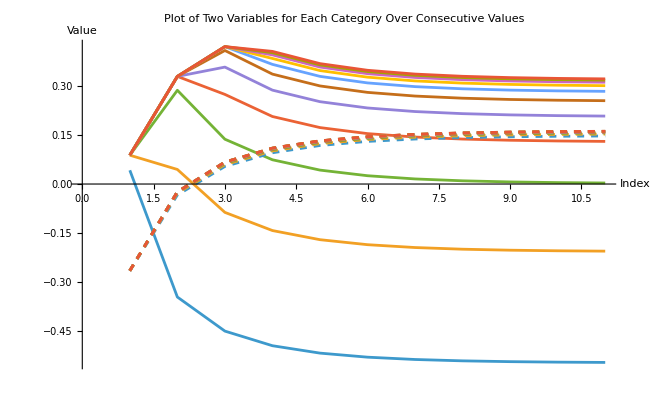

```mathematica
ehungprev=resprev
euptprev =resprev2
colorblindSafeColors=Table[ColorData["ColorBlindSafe"][i],{i,11}];

plot1=ListLinePlot[ehungprev,PlotStyle->colorblindSafeColors,PlotLegends->None];

plot2=ListLinePlot[euptprev,PlotStyle->Table[{Dashed,colorblindSafeColors[[i]]},{i,11}],PlotLegends->None];

(*Combine the plots and add legends*)
Show[plot1,plot2,PlotLegends->Placed[LineLegend[Flatten[Table[{Style["Category "<>ToString[i]<>" (solid)",colorblindSafeColors[[i]]],Style["Category "<>ToString[i]<>" (dashed)",Dashed,colorblindSafeColors[[i]]]},{i,11}]],LegendFunction->"Frame"],Below],AxesLabel->{"Index","Value"},PlotLabel->"Plot of Two Variables for Each Category Over Consecutive Values"]
```

ColorData::notent: ColorBlindSafe is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

Part::partw: Part {1,3,5,7,9,11} of ColorData[ColorBlindSafe,ColorList] does not exist.

Part::partw: Part 3 of ColorData[ColorBlindSafe,ColorList]⟦{1,3,5,7,9,11}⟧ does not exist.

Part::partw: Part 4 of ColorData[ColorBlindSafe,ColorList]⟦{1,3,5,7,9,11}⟧ does not exist.

Part::partw: Part 5 of ColorData[ColorBlindSafe,ColorList]⟦{1,3,5,7,9,11}⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of ColorData[ColorBlindSafe,ColorList]⟦{1,3,5,7,9,11}⟧ does not exist.

Part::partw: Part 4 of ColorData[ColorBlindSafe,ColorList]⟦{1,3,5,7,9,11}⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

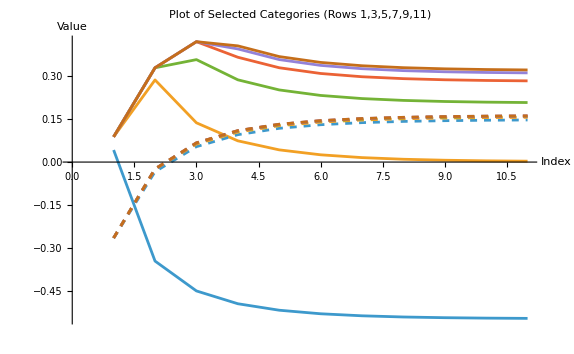

```mathematica
(*Select rows 1,3,5,7,9,11 from each matrix*)selectedRows={1,3,5,7,9,11};
ehungprevSub=resprev[[selectedRows]];
euptprevSub=resprev2[[selectedRows]];

(*Get colorblind-safe palette*)
colorblindSafeColors=ColorData["ColorBlindSafe","ColorList"];
colorSub=colorblindSafeColors[[selectedRows]];

(*Plot the solid and dashed lines*)
plot1=ListLinePlot[ehungprevSub,PlotStyle->colorSub,PlotLegends->None];

plot2=ListLinePlot[euptprevSub,PlotStyle->Table[{Dashed,colorSub[[i]]},{i,Length[selectedRows]}],PlotLegends->None];

(*Combine and add legend*)
Show[plot1,plot2,PlotLegends->Placed[LineLegend[Flatten[Table[{Style["Category "<>ToString[selectedRows[[i]]]<>" (solid)",colorSub[[i]]],Style["Category "<>ToString[selectedRows[[i]]]<>" (dashed)",Dashed,colorSub[[i]]]},{i,Length[selectedRows]}]],LegendFunction->"Frame"],Below],AxesLabel->{"Index","Value"},PlotLabel->"Plot of Selected Categories (Rows 1,3,5,7,9,11)"]
```